```mathematica
Clear[x]; Clear[u]; Clear[t];
```

```mathematica
F[k_]:=Exp[I*k*x-u*k*t]/k^2
```

```mathematica
Expand[F[k]]
```

ⅇ^(-k t u+ⅈ k x)/k^2

```mathematica
Integrate[F[k],{k,Infinity,Infinity}]
```

0

```mathematica
x=1; u=0.5; t=5;
```

```mathematica
G[k_]:=Cos[k*x]*Exp[-u*t*k]/k^2
```

```mathematica
Expand[G[k]]
```

(ⅇ^(-2.5 k) Cos[k])/k^2

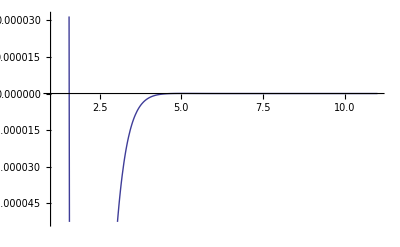

```mathematica
Plot[G[k],{k,1,11}]
```

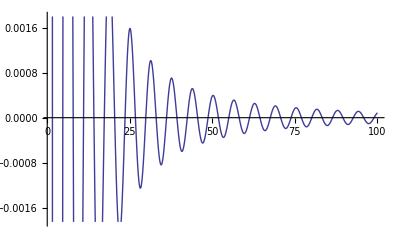

```mathematica
Plot[Cos[k]/k^2,{k,1,100}]
```